Get::noopen: Cannot open Project_rand_card.nb.

$Failed

Get::noopen: Cannot open calcolaProb.nb.

$Failed

Inserisci il numero di giocatori:

$Canceled

Inserisci il numero di carte scoperte:

$Canceled

Set::shape: Lists {carteBanco,carteGiocatore} and randomCards[$Canceled] are not the same shape.

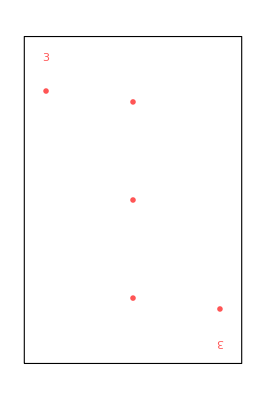
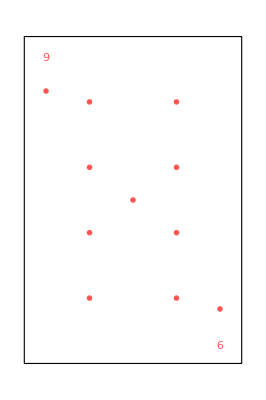
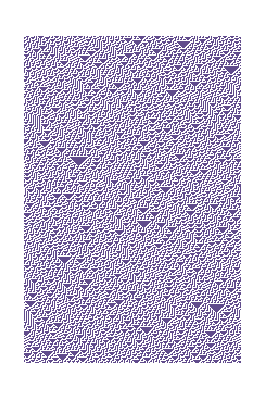
-Graphics--Graphics--Graphics--Graphics--Graphics-

-Graphics-

Row

print[qual'è la probabilità di fare coppia per il giocatore 1?]

scegli la probabilita

$Canceled

```mathematica
Get["Project_rand_card.nb"]
Get["calcolaProb.nb"]
Print["Inserisci il numero di giocatori: "]
player=Input[]
Print["Inserisci il numero di carte scoperte: "]
carteScoperte=Input[]

{carteBanco, carteGiocatore}=randomCards[carteScoperte];
carteBanco
carteGiocatore

print["qual'è la probabilità di fare coppia per il giocatore 1?"]
Print["scegli la probabilita"]
modalita=Input[]
probabilita = calcolaProb[carteBanco, carteGiocatore, player, modalita];
```